```mathematica
αcont=SetPrecision[{0.5137193759431391,0.0024666827878353577},100]; 
σcont=SetPrecision[{0.16955497884544793,0.0008581023195660334},100];
```

### Complex permittivity in real space

```mathematica
Assuming[{a∈Reals,a>0,mD∈Reals,mD>0,r∈Reals,r>0},Integrate[p^4/(p^2+mD^2)Exp[-a p]Sinc[p r],{p,0,∞}]]/.a->0//FullSimplify
```

(mD^2 (-ⅈ Cosh[mD r] (Log[-ⅈ mD r]-Log[ⅈ mD r])+π Sinh[mD r]))/(2 r)

```mathematica
Assuming[{mD∈Reals,mD>0,r∈Reals,r>0},Integrate[(p^3 mD^2)/((p^2+mD^2)^2)Sinc[p r],{p,0,∞}]]//FullSimplify
```

(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(2 r)

```mathematica
ϵ[r_,mD_,α_,T_]:=α/π((mD^2 (-ⅈ Cosh[mD r] (Log[-ⅈ mD r]-Log[ⅈ mD r])+π Sinh[mD r]))/r-ⅈ T(mD π^(3/2) MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/r);
```

```mathematica
ϵp[p_,mD_,T_]:=p^2/(p^2+mD^2)-ⅈ π T(p mD^2)/((p^2+mD^2)^2);
```

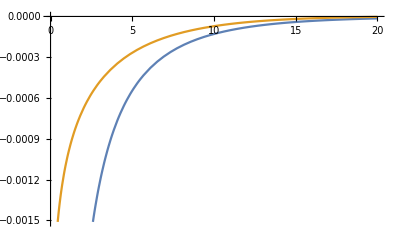

```mathematica
Plot[{Re[ϵ[x,15/100,αcont[[1]],155/1000]],Im[ϵ[x,15/100,αcont[[1]],155/1000]]},{x,0,20}]
```

## Checking Debye - Huckel solutions

### Coulomb Real

```mathematica
ReVc0[r_,mD_,α_]:=-α Exp[-mD r]/r;
```

```mathematica
D[-α Exp[-mD r]/r,{r,2}]+2/r D[-α Exp[-mD r]/r,r]//FullSimplify
```

-(ⅇ^(-mD r) mD^2 α)/r

```mathematica
ReVc0lhs[r_,mD_,α_,T_]:=-(ⅇ^(-mD r) mD^2 α)/r;
```

```mathematica
ReVc0lhs[10,15/100,αcont[[1]],155/1000]
```

-0.00025790914490747412933295853232803434492188450090156368952747755118347254111501423943563572545990349601919257318840316743478589713623793728548079159489306906225992500796743170010926100592209328972073333481243948550292368539899222689218675363410565598418721506542516332364356694732058314120825336679327079260965232219947654790202309244504581650263354101782071704710981151382263457903660787334784934648110187174097945462531394900463185247831470705896106782554414656410037119028988217772015600419264525862

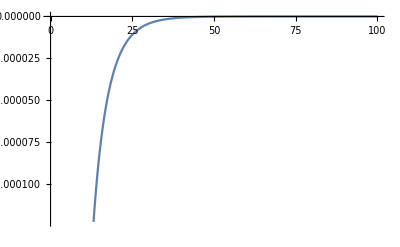

```mathematica
Plot[ReVc0lhs[r,15/100,αcont[[1]],155/1000],{r,10^-10,100}]
```

```mathematica
Plot[Re[ϵ[r,15/100,αcont[[1]],155/1000]],{r,10^-10,100}]
```

-Graphics-

```mathematica
N[ReVc0lhs[10,15/100,αcont[[1]],155/1000],100]
```

-0.000257909144907474129332958532328034344921884500901563689527477551183472541115014239435635725459903496

```mathematica
N[Re[ϵ[10,15/100,αcont[[1]],155/1000]],100]
```

-0.000257909144907474129332958532328034344921884500901563689527477551183472541115014239435635725459903496

### Coulomb Imag

```mathematica
ImVc0[r_,mD_,α_,T_]:=-α T Quiet[NIntegrate[2 z/((z^2+1)^2)Sinc[mD r z],{z,0,∞}]];
```

```mathematica
D[Sinc[mD r z],{r,2}]+2/r D[Sinc[mD r z],r]
```

mD z (-(2 Cos[mD r z])/(mD r^2 z)-Sin[mD r z]/r+(2 Sin[mD r z])/(mD^2 r^3 z^2))+(2 mD z (Cos[mD r z]/(mD r z)-Sin[mD r z]/(mD^2 r^2 z^2)))/r

```mathematica
ImVc0lhs[r_,mD_,α_,T_]:=α T NIntegrate[2 z/((z^2+1)^2)(mD z Sin[mD r z])/r,{z,0,∞},MaxRecursion->20,WorkingPrecision->100];
```

```mathematica
ImVc0lhs[10^-10,15/100,αcont[[1]],155/1000]
```

0.08902712752574571758686368359075926488713039882270125961123640795616224852224639456980014087627809165

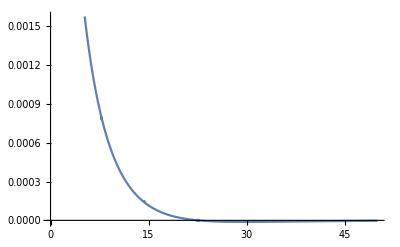

```mathematica
Plot[ImVc0lhs[r,15/100,αcont[[1]],155/1000],{r,10^-10,50}]
```

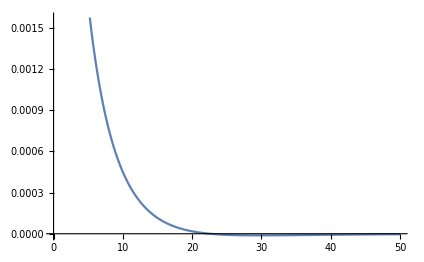

```mathematica
Plot[-Im[ϵ[r,15/100,αcont[[1]],155/1000]],{r,0,50}]
```

```mathematica
N[ImVc0lhs[10,15/100,αcont[[1]],155/1000],100]
```

0.0004492926428964755177926724481249883499533506225364057136602993694003095244861282567840744669340077323

```mathematica
N[Im[ϵ[10,15/100,αcont[[1]],155/1000]],100]
```

-0.0004492926428964755177926724481249883499533506225364057476349410209992435376005007923033479865840584338

### String Real

```mathematica
ReVs0[r_,mD_,α_,σ_]:=Gamma[1/4]/(2^(3/4)√π)σ/((mD^2 σ/α)^(1/4)) ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((mD^2 σ/α)^(1/4));
```

```mathematica
-1/r^2 D[ReVs0[r,mD,α,σ],{r,2}]//FullSimplify
```

(σ Gamma[5/4] (-2 α ((mD^2 σ)/α)^(3/4) Hypergeometric0F1Regularized[3/4,(mD^2 r^4 σ)/(16 α)]+mD^2 r σ Hypergeometric0F1Regularized[5/4,(mD^2 r^4 σ)/(16 α)]))/α

```mathematica
ReVs0lhs[r_,mD_,α_,σ_]:=(σ Gamma[5/4] (-2 α ((mD^2 σ)/α)^(3/4) Hypergeometric0F1Regularized[3/4,(mD^2 r^4 σ)/(16 α)]+mD^2 r σ Hypergeometric0F1Regularized[5/4,(mD^2 r^4 σ)/(16 α)]))/α;
```

```mathematica
ReVs0lhs[10,15/100,αcont[[1]],σcont[[1]]]
```

-0.0000337668110559217912487337964045669971869772473182621932086458641531040003137506634696529473847329023844417937919906613573802395846470103707712832193032698373754055292762592414284371597372834579724022184107368362188700659896067915167730869819788112714390631293472365673408726811386555608694871015948879901683818062329125189736415897991152324935024822818774096965021386879307383557918027179717812170861860305978344310369672478661251337779917687270714678694717942066998680689693564716343988753410449

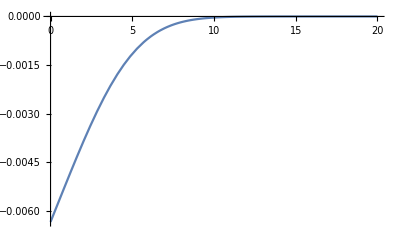

```mathematica
Plot[ReVs0lhs[r,15/100,αcont[[1]],σcont[[1]]],{r,10^-10,20}]
```

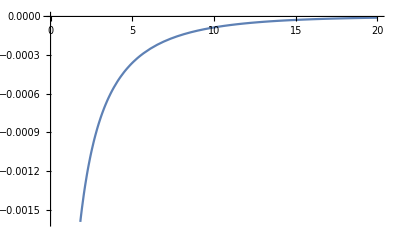

```mathematica
Plot[Re[ϵ[r,15/100,σcont[[1]],0]],{r,10^-10,20}]
```

```mathematica
N[ReVs0lhs[5,15/100,αcont[[1]],σcont[[1]]],100]
```

-0.001156434385302800828382266322219653953736387599213656402626157371007784542295014234663072038099403034

```mathematica
N[Re[ϵ[5,15/100,σcont[[1]],0]],100]
```

-0.0003604144538578496044324751525895156800790899482466618905657921948534146105685928203264966577987873229

### String Imag

## Attempt to solve for String part

### Real

#### Analytic

```mathematica
Integrate[-σ/π r mD^2 (-ⅈ Cosh[mD r] (Log[-ⅈ mD r]-Log[ⅈ mD r])+π Sinh[mD r]),r]//FullSimplify
```

(-σ Cosh[mD r] (mD π r+ⅈ Log[-ⅈ mD r]-ⅈ Log[ⅈ mD r])+σ (π+ⅈ mD r (Log[-ⅈ mD r]-Log[ⅈ mD r])) Sinh[mD r])/π

```mathematica
ϵ1an[r_,mD_,σ_]:=Re[(-σ Cosh[mD r] (mD π r+ⅈ Log[-ⅈ mD r]-ⅈ Log[ⅈ mD r])+σ (π+ⅈ mD r (Log[-ⅈ mD r]-Log[ⅈ mD r])) Sinh[mD r])/π];
```

```mathematica
ϵ1an[100,15/100,σcont[[1]]]
```

-8.2987618370336806148121689622396113980692940689561425123313826721934075124434231176813×10^-7

```mathematica
ϵ1an[800,15/100,σcont[[1]]]
```

0.

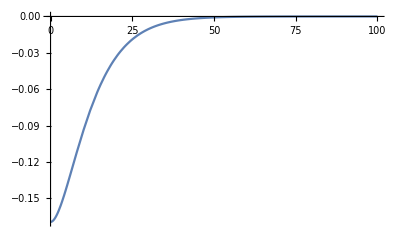

```mathematica
Plot[ϵ1an[r,15/100,σcont[[1]]],{r,0,100},PlotRange->All]
```

```mathematica
Integrate[(-σ Cosh[mD r] (mD π r+ⅈ Log[-ⅈ mD r]-ⅈ Log[ⅈ mD r])+σ (π+ⅈ mD r (Log[-ⅈ mD r]-Log[ⅈ mD r])) Sinh[mD r])/π,r]
```

(σ (Cosh[mD r] (2 π+ⅈ mD r Log[-ⅈ mD r]-ⅈ mD r Log[ⅈ mD r])-(mD π r+2 ⅈ Log[-ⅈ mD r]-2 ⅈ Log[ⅈ mD r]) Sinh[mD r]))/(mD π)

```mathematica
ϵ2an[r_,mD_,σ_]:=Re[σ/(mD π)(Cosh[mD r] (2 π+ⅈ mD r Log[-ⅈ mD r]-ⅈ mD r Log[ⅈ mD r])-(mD π r+2 ⅈ Log[-ⅈ mD r]-2 ⅈ Log[ⅈ mD r]) Sinh[mD r])];
```

```mathematica
ϵ2an[350,15/100,σcont[[1]]]
```

9.753387754313067062467543001796648522817837798231323269589740629896118859420725298821183550362581431×10^-22

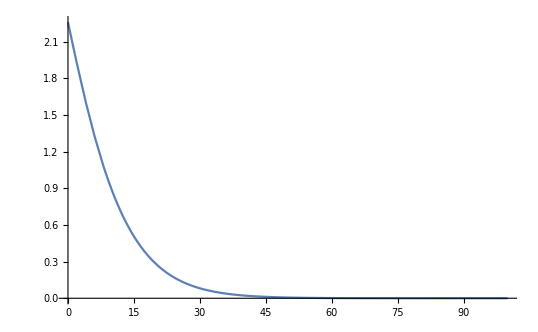

```mathematica
Plot[ϵ2an[r,15/100,σcont[[1]]],{r,0,100},PlotRange->All]
```

```mathematica
ReVs0an[r_,mD_,σ_]:=ϵ2an[r,mD,σ]
```

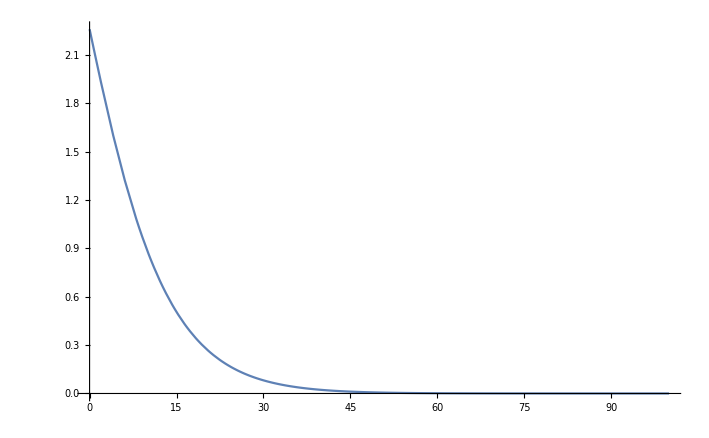

```mathematica
Plot[ReVs0an[r,15/100,σcont[[1]]],{r,0,100},PlotRange->All]
```

```mathematica
ReVs0an[10^-10,15/100,σcont[[1]]]
```

2.260733051255683555050157608016607631061953830783071759835480567097439547828010245951437860699503116

```mathematica
ReVsold[r_,mD_,α_,σ_]:=Gamma[1/4]/(2^(3/4)√π)σ/((mD^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]+Gamma[1/4]/(2 Gamma[3/4])σ/((mD^2 σ/α)^(1/4));
```

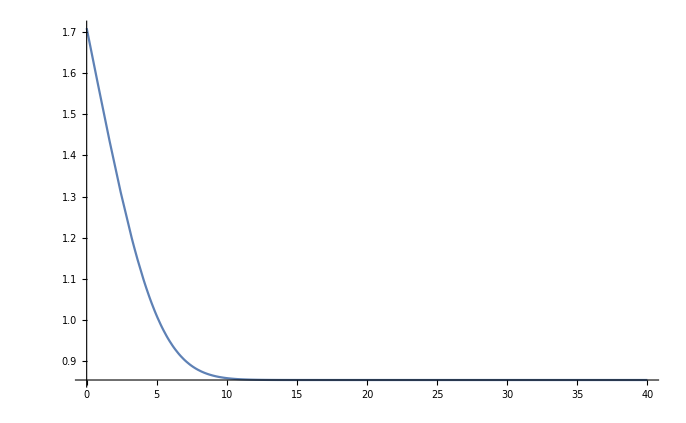

```mathematica
Plot[ReVsold[r,15/100,αcont[[1]],σcont[[1]]],{r,0,40},PlotRange->All]
```

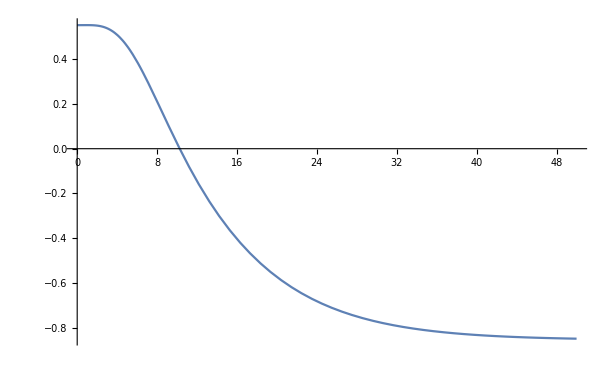

```mathematica
Plot[ReVs0an[r,15/100,σcont[[1]]]-ReVsold[r,15/100,αcont[[1]],σcont[[1]]],{r,0,50},PlotRange->All]
```

```mathematica
(*check nummerically that solution holds*)
```

```mathematica
checktab=ParallelTable[{r,ReVs0an[r,15/100,σcont[[1]]]},{r,10^-10,350}];
```

```mathematica
checkinter=Interpolation[checktab];
```

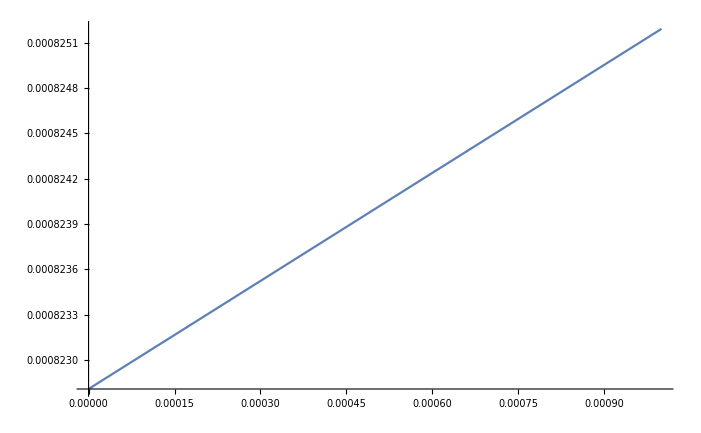

```mathematica
Plot[checkinter''[x],{x,0,0.001},PlotRange->All]
```

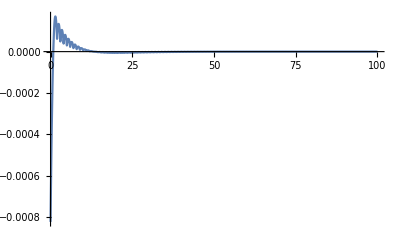

```mathematica
Plot[-checkinter''[x]-x^2 Re[ϵ[x,15/100,σcont[[1]],0]],{x,0,100},PlotRange->All]
```

#### Numeric

```mathematica
ϵ1[r_,mD_,σ_,T_]:=NIntegrate[-r1^2 Re[ϵ[r1,mD,σ,T]],{r1,0,r},WorkingPrecision->10];
```

```mathematica
ϵ1[100,15/100,σcont[[1]],0]
```

0.1695027537

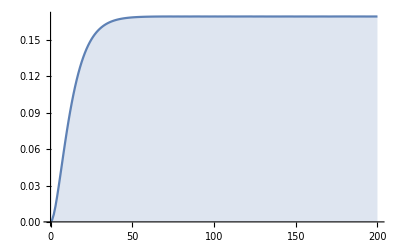

```mathematica
DiscretePlot[ϵ1[r,15/100,σcont[[1]],0],{r,0,200}]
```

```mathematica
ϵ1tab=ParallelTable[{r,ϵ1[r,15/100,σcont[[1]],0]},{r,0,200,1/100}];
```

```mathematica
ϵ1inter=Interpolation[ϵ1tab];
```

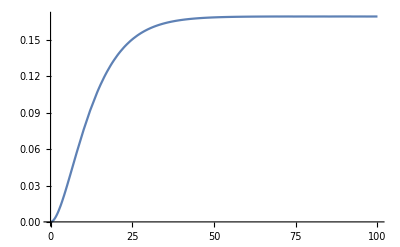

```mathematica
Plot[ϵ1inter[x],{x,0,100},PlotRange->All]
```

```mathematica
ϵ2[r_]:=NIntegrate[ϵ1inter[r1],{r1,0,r}];
```

```mathematica
ϵ2[100]
```

14.6935

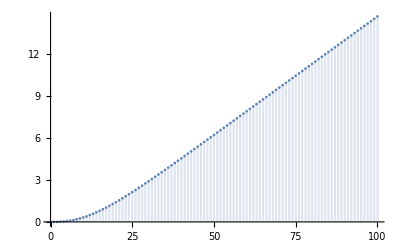

```mathematica
DiscretePlot[ϵ2[r],{r,0,100}]
```

### Imaginary

#### Analytic

```mathematica
-σ mD √π T Integrate[r  MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4],r]//FullSimplify
```

-(2 √π T σ MeijerG[{{1/2},{}},{{3/2,3/2},{0}},(mD^2 r^2)/4])/mD

```mathematica
ϵ1ani[r_,mD_,σ_,T_]:=-2 √π (T σ)/mD MeijerG[{{1/2},{}},{{3/2,3/2},{0}},(mD^2 r^2)/4];
```

```mathematica
Limit[Series[MeijerG[{{1/2},{}},{{3/2,3/2},{0}},r],{r,0,3}],r->0]
```

0

```mathematica
Limit[Series[MeijerG[{{1/2},{}},{{3/2,3/2},{0}},r],{r,∞,3}],r->∞]
```

0

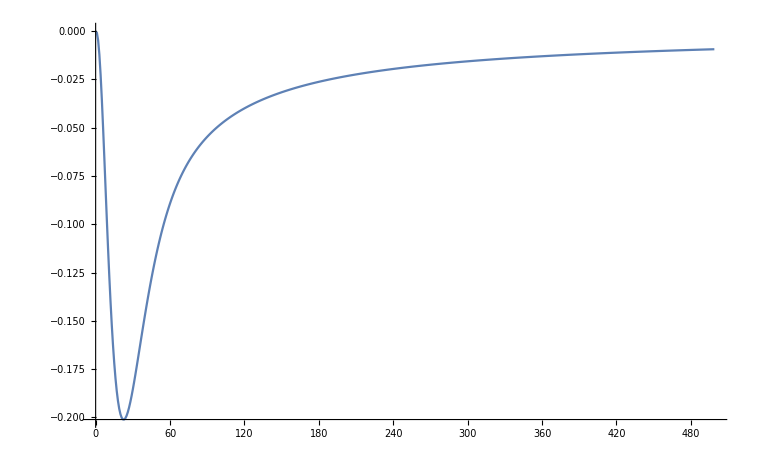

```mathematica
DiscretePlot[ϵ1ani[r,15/100,σcont[[1]],155/1000],{r,10^-30,500},PlotRange->All,Joined->True,Filling->None,PlotRange->All]
```

```mathematica
-2 √π (T σ)/mD Integrate[MeijerG[{{1/2},{}},{{3/2,3/2},{0}},(mD^2 r^2)/4],r]
```

-(√π r T σ MeijerG[{{1/2,1/2},{}},{{3/2,3/2},{-1/2,0}},(mD^2 r^2)/4])/mD

```mathematica
ϵ2ani[r_,mD_,σ_,T_]:=-√π r (T σ)/mD MeijerG[{{1/2,1/2},{}},{{3/2,3/2},{-1/2,0}},(mD^2 r^2)/4];
```

```mathematica
Limit[Series[x MeijerG[{{1/2,1/2},{}},{{3/2,3/2},{-1/2,0}},x^2],{x,0,3}],x->0]
```

0

```mathematica
Series[x MeijerG[{{1/2,1/2},{}},{{3/2,3/2},{-1/2,0}},x^2],{x,∞,3}]//FullSimplify
```

ⅇ^(-2 x) (ⅈ √π x^2+3/2 ⅈ √π x+ⅈ √π+O[1/x]^3)+((2 (-1+EulerGamma+Log[2]-Log[1/x]))/(√π)-2/(√π x^2)+O[1/x]^3)

```mathematica
Block[{$MaxExtraPrecision = 5000},N[ϵ2ani[10^4,15/100,σcont[[1]],155/1000]]]
```

-32.1934

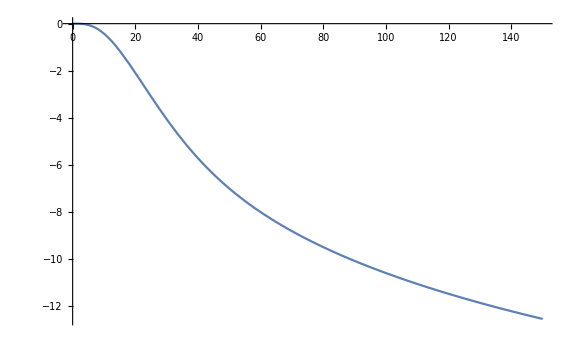

```mathematica
Plot[ϵ2ani[r,15/100,σcont[[1]],155/1000],{r,0,150},PlotRange->All]
```

```mathematica
ImVs0an[r_,mD_,σ_,T_]:=ϵ2ani[r,mD,σ,T];
```

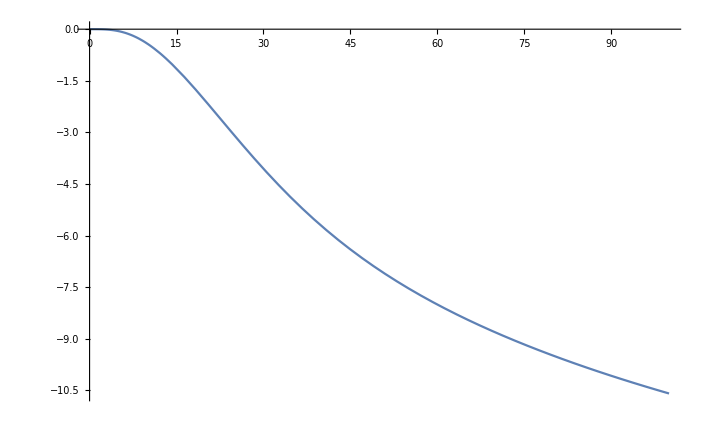

```mathematica
Plot[ImVs0an[r,15/100,σcont[[1]],155/1000],{r,0,100},PlotRange->All]
```

```mathematica
g[s_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p s],{p,0,∞}]];
```

```mathematica
ImVsold[r_,mD_,α_,σ_,T_]:=-α T (ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 s]] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,(mD^2 σ/α)^(1/4)r},MaxRecursion->20,WorkingPrecision->10]]+Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,(mD^2 σ/α)^(1/4)r,∞},MaxRecursion->20,WorkingPrecision->10]]);
```

```mathematica
ImVsold[0,15/100,αcont[[1]],σcont[[1]],155/1000]
```

-0.1551035946

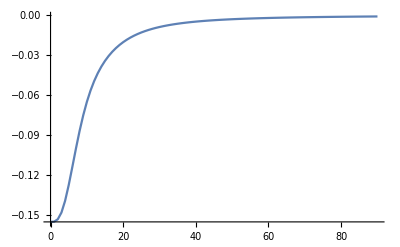

```mathematica
DiscretePlot[ImVsold[r,15/100,αcont[[1]],σcont[[1]],155/1000],{r,0,90},PlotRange->All,Joined->True,Filling->None]
```

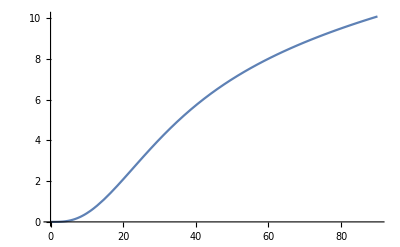

```mathematica
Plot[-ImVs0an[r,15/100,σcont[[1]],155/1000],{r,0,90},PlotRange->All]
```

## Discretization

```mathematica
rmax=50.;
dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
```

```mathematica
one[n_,d_]:=DiagonalMatrix[1+0 Range[n-Abs[d]],d];
stringopgauss=(one[len,-1]-2 one[len,0]+one[len,1]);
coulopgauss=1/dr^2(one[len,-1]-2 one[len,0]+one[len,1])-2/dr(one[len,-1]+one[len,1]);
```

```mathematica
{vals,vecs}=Eigensystem[N[coulopgauss]];
```

```mathematica
U=Transpose[vecs];
```

```mathematica
eigeninter=Interpolation[Transpose[{rlist,vals}]];
```

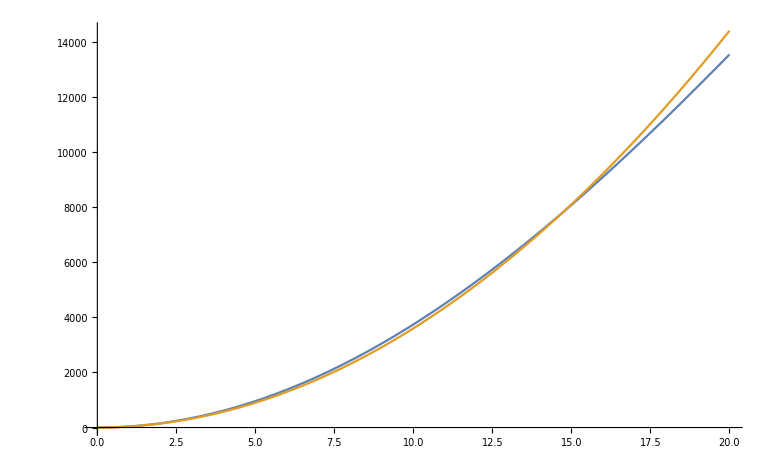

```mathematica
Plot[{eigeninter[x]-eigeninter[0.01],36 x^2},{x,0.01,20}]
```

```mathematica
eigeninter[0.01]
```

-39600.

```mathematica
deltatrans=Inverse[U].Array[KroneckerDelta,{len,len}].U;
```

```mathematica
deltatrans[[;;10,;;10]]//MatrixForm
```

(1. | -5.80876×10^-17 | 1.04238×10^-16 | 6.62434×10^-17 | -1.03226×10^-16 | 1.1082×10^-16 | 1.0156×10^-16 | -1.68226×10^-16 | 2.55607×10^-17 | -2.75792×10^-17
-1.74365×10^-17 | 1. | 3.11227×10^-16 | 2.72464×10^-17 | -2.17113×10^-16 | -1.58124×10^-17 | 1.00518×10^-16 | -1.03131×10^-16 | -6.52051×10^-17 | -5.90871×10^-17
-2.45738×10^-16 | -1.22916×10^-16 | 1. | -8.62118×10^-17 | 1.48646×10^-16 | -2.38409×10^-16 | 2.56982×10^-16 | -1.87026×10^-16 | 2.50416×10^-17 | 1.17731×10^-16
-1.32565×10^-16 | -1.79228×10^-16 | -5.0772×10^-17 | 1. | -4.48544×10^-17 | 1.4158×10^-16 | -7.16299×10^-16 | 2.5158×10^-16 | -2.23395×10^-16 | -3.20413×10^-16
1.17071×10^-17 | 2.04956×10^-17 | -1.05491×10^-16 | 7.85139×10^-17 | 1. | 4.51282×10^-16 | -9.03782×10^-17 | -2.22422×10^-17 | -1.39228×10^-16 | -2.90996×10^-16
-1.12999×10^-16 | -7.64856×10^-17 | -4.6572×10^-17 | -7.52168×10^-17 | -2.55169×10^-17 | 1. | 5.22621×10^-16 | -4.27885×10^-17 | 2.25876×10^-16 | -2.39895×10^-16
-7.10187×10^-17 | -7.04234×10^-18 | 1.22721×10^-17 | -1.16218×10^-16 | -1.4239×10^-17 | 4.56957×10^-17 | 1. | -2.89332×10^-17 | -2.00538×10^-16 | 2.60841×10^-16
1.43627×10^-17 | 4.85885×10^-17 | 8.8808×10^-17 | 2.63743×10^-17 | -6.55896×10^-17 | 8.52058×10^-17 | 1.99118×10^-17 | 1. | -2.67995×10^-16 | 1.4374×10^-16
5.89229×10^-17 | 2.67398×10^-17 | -4.31108×10^-18 | 7.16899×10^-17 | -1.40989×10^-17 | 2.10035×10^-17 | 7.08967×10^-19 | -9.07249×10^-17 | 1. | 4.09604×10^-17
-3.7226×10^-18 | 4.66585×10^-17 | -1.06025×10^-17 | -2.60081×10^-18 | -2.72582×10^-17 | 6.00673×10^-18 | -2.68298×10^-17 | 7.09352×10^-17 | -3.91871×10^-17 | 1.)

```mathematica
ϵdis=DiagonalMatrix[Table[ϵ[r],{r,dr,rmax,dr}]];
```

```mathematica
ϵdistra=Inverse[U].ϵdis.U;
```

```mathematica
ϵdistra1=U.ϵdis.Inverse[U];
```

```mathematica
ϵdistra[[;;10,;;10]]//MatrixForm
```

(-0.00146953+0.00442974 ⅈ | -0.0014631+0.00392421 ⅈ | 0.00108758-0.00219177 ⅈ | 0.000850564-0.00132663 ⅈ | -0.000688219+0.000863331 ⅈ | 0.000579548-0.000611518 ⅈ | 0.000498112-0.000449632 ⅈ | -0.000437747+0.000347716 ⅈ | 0.000389451-0.000274194 ⅈ | 0.00035131-0.000223558 ⅈ
-0.0014631+0.00392421 ⅈ | -0.00255711+0.0066215 ⅈ | 0.00231366-0.00525084 ⅈ | 0.0017758-0.0030551 ⅈ | -0.00143011+0.00193814 ⅈ | 0.00118633-0.00131296 ⅈ | 0.0010173-0.000959234 ⅈ | -0.000887563+0.000723826 ⅈ | 0.000789058-0.000571274 ⅈ | 0.000708921-0.000458486 ⅈ
0.00108758-0.00219177 ⅈ | 0.00231366-0.00525084 ⅈ | -0.00324533+0.00748484 ⅈ | -0.00289321+0.00586235 ⅈ | 0.00227391-0.00350473 ⅈ | -0.00186786+0.00228586 ⅈ | -0.00157578+0.00158716 ⅈ | 0.00136861-0.00118279 ⅈ | -0.00120703+0.000908118 ⅈ | -0.00108231+0.000726885 ⅈ
0.000850564-0.00132663 ⅈ | 0.0017758-0.0030551 ⅈ | -0.00289321+0.00586235 ⅈ | -0.00374344+0.00793447 ⅈ | 0.00333096-0.00621007 ⅈ | -0.00266336+0.00377892 ⅈ | -0.00221917+0.00250942 ⅈ | 0.00189525-0.00177145 ⅈ | -0.00166186+0.0013384 ⅈ | -0.00147775+0.00104037 ⅈ
-0.000688219+0.000863331 ⅈ | -0.00143011+0.00193814 ⅈ | 0.00227391-0.00350473 ⅈ | 0.00333096-0.00621007 ⅈ | -0.0041329+0.00820866 ⅈ | 0.00368227-0.00643363 ⅈ | 0.00298283-0.00396322 ⅈ | -0.00251242+0.00266503 ⅈ | 0.00216597-0.0019037 ⅈ | 0.00191347-0.00145288 ⅈ
0.000579548-0.000611518 ⅈ | 0.00118633-0.00131296 ⅈ | -0.00186786+0.00228586 ⅈ | -0.00266336+0.00377892 ⅈ | 0.00368227-0.00643363 ⅈ | -0.00445237+0.00839295 ⅈ | -0.00397552+0.00658924 ⅈ | 0.00325355-0.00409547 ⅈ | -0.00276404+0.00277951 ⅈ | -0.00240081+0.00200319 ⅈ
0.000498112-0.000449632 ⅈ | 0.0010173-0.000959234 ⅈ | -0.00157578+0.00158716 ⅈ | -0.00221917+0.00250942 ⅈ | 0.00298283-0.00396322 ⅈ | -0.00397552+0.00658924 ⅈ | -0.00472309+0.00852521 ⅈ | 0.00422714-0.00670372 ⅈ | -0.00348839+0.00419496 ⅈ | -0.00298434+0.00286723 ⅈ
-0.000437747+0.000347716 ⅈ | -0.000887563+0.000723826 ⅈ | 0.00136861-0.00118279 ⅈ | 0.00189525-0.00177145 ⅈ | -0.00251242+0.00266503 ⅈ | 0.00325355-0.00409547 ⅈ | 0.00422714-0.00670372 ⅈ | -0.00495792+0.00862469 ⅈ | 0.00444744-0.00679144 ⅈ | 0.00369573-0.00427249 ⅈ
0.000389451-0.000274194 ⅈ | 0.000789058-0.000571274 ⅈ | -0.00120703+0.000908118 ⅈ | -0.00166186+0.0013384 ⅈ | 0.00216597-0.0019037 ⅈ | -0.00276404+0.00277951 ⅈ | -0.00348839+0.00419496 ⅈ | 0.00444744-0.00679144 ⅈ | -0.00516526+0.00870223 ⅈ | -0.00464335+0.00686079 ⅈ
0.00035131-0.000223558 ⅈ | 0.000708921-0.000458486 ⅈ | -0.00108231+0.000726885 ⅈ | -0.00147775+0.00104037 ⅈ | 0.00191347-0.00145288 ⅈ | -0.00240081+0.00200319 ⅈ | -0.00298434+0.00286723 ⅈ | 0.00369573-0.00427249 ⅈ | -0.00464335+0.00686079 ⅈ | -0.00535085+0.00876434 ⅈ)

```mathematica
ϵdis1=ParallelTable[ϵ[r],{r,dr,rmax,dr}];
```

```mathematica
ϵdisp1=Fourier[ϵdis1];
```

```mathematica
ϵdisp=ParallelTable[ϵp[p],{p,-1,1,0.001}];
```

```mathematica
ϵdisp2=Fourier[ϵdisp]
```

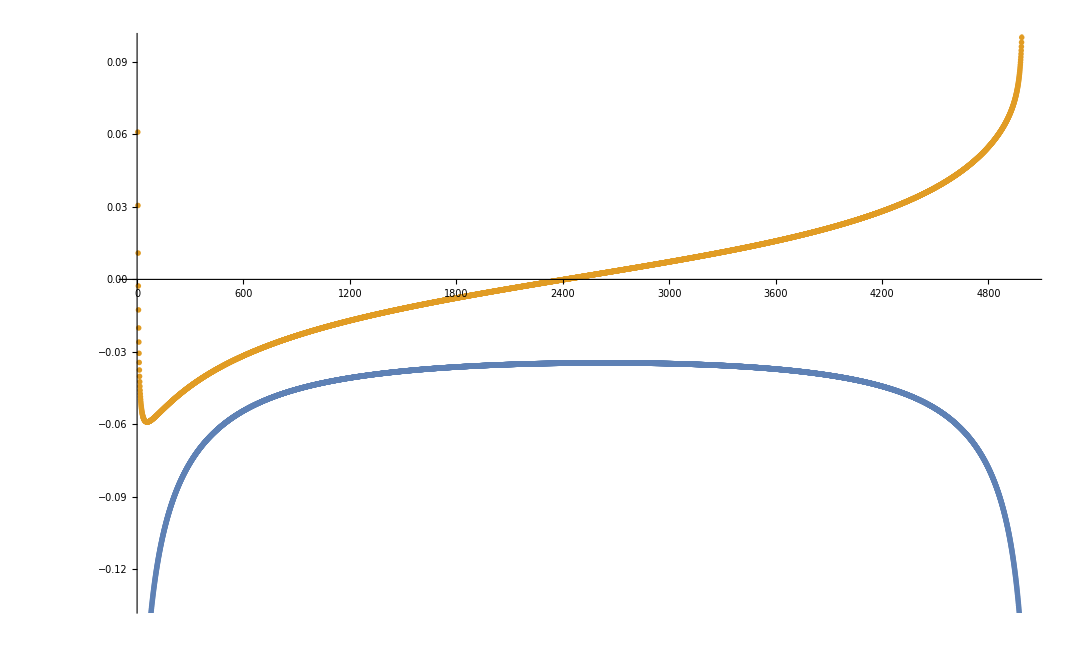

```mathematica
ListPlot[{Re[ϵdisp1],Im[ϵdisp1]}]
```

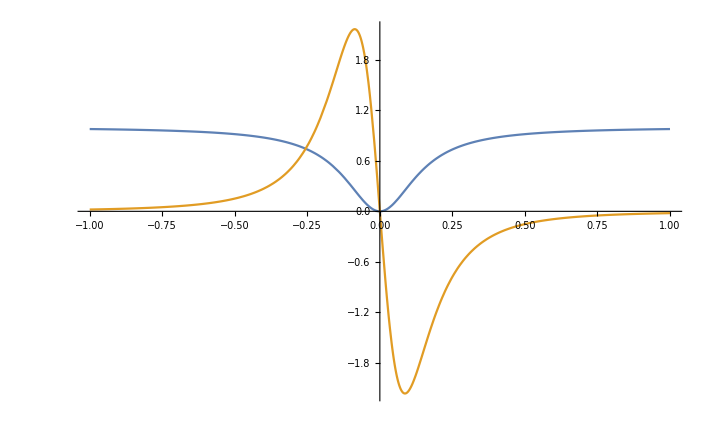

```mathematica
Plot[{p^2/(p^2+mD^2),-(p mD^2)/((p^2+mD^2)^2)},{p,-1,1}]
```